```mathematica
Clear[ab, ba, kt,u, d,rs, a, b, rho,rho1,rho2,rho3, rhodash, rhodash1, rhodash2,rhodash3, lgs, lgs1,lgs2, lgs3,lgs4,lgs5,lgs6]
```

```mathematica
kt = 1;
d = 0.05;
rs = 1;
a = 4;
b = 6;
u=1;
```

```mathematica
4
```

4

```mathematica
w = {{-ab,ba},{ab,-ba}};
```

```mathematica
evec = Eigenvectors[w]
```

{{ba/ab,1},{-1,1}}

```mathematica
s = Transpose[{Normalize[evec[[1]]],Normalize[evec[[2]]]}] ;
```

```mathematica
invs = Simplify[Assuming[{ab>0, ba>0},Inverse[s]]];
```

```mathematica
diagw = Simplify[invs.w.s]
```

{{0,0},{0,-ab-ba}}

```mathematica
bcu = {{1,0},{0,Exp[u/kt]}};
```

```mathematica
rhodash[r_] = {{1, 1/r, 0, 0},{0, 0, Exp[-Sqrt[Abs[diagw[[2,2]]]/d]r]/r,Exp[Sqrt[Abs[diagw[[2,2]]]/d]r]/r}}
```

{{1,1/r,0,0},{0,0,ⅇ^(-4.47214 r √Abs[-ab-ba])/r,ⅇ^(4.47214 r √Abs[-ab-ba])/r}}

```mathematica
lgs1 = Join[rhodash[rs],{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},2];
lgs2 = Join[rhodash[a], -invs.bcu.s.rhodash[a], {{0,0,0,0},{0,0,0,0}},2];
lgs3 = Join[rhodash'[a],-rhodash'[a],{{0,0,0,0},{0,0,0,0}},2];
lgs4= Join[{{0,0,0,0},{0,0,0,0}},invs.bcu.s.rhodash[b],-rhodash[b],2];
lgs5 = Join[{{0,0,0,0},{0,0,0,0}},rhodash'[b],-rhodash'[b],2];
lgs6 = Join[{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0},{0,0,0,Infinity}},2];
```

```mathematica
lgs = Join[lgs1, lgs2, lgs3, lgs4,lgs5,lgs6,1];
```

```mathematica
lgs = lgs[[1;;11,1;;11]];
```

```mathematica
ab = 1;
 ba = 1;
```

```mathematica
c =Assuming[{ab>0, ba>0,d>0,kt>0,b>a>rs>0}, LinearSolve[lgs,Transpose[{{0,0,0,0,0,0,0,0,0,0,1}}]]];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1., 1., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0.00179176, 558.11, 0., 0., 0., 0., 0., 0., 0.}, « 7 », {0., 0., 0., 0., 0., 0., -3.5798×10^-17, 3.10168×10^16, 0., 0., 3.5798×10^-17}, {0., 0., 0., 0., 0., 0., 0., 0., 1., 0., 0.}} may contain significant numerical errors.

```mathematica
c = Assuming[b > a > rs > 0,Simplify[c]];
```

```mathematica
c = Join[c,{{0}}];
```

```mathematica
Simplify[lgs.c[[1;;11]]]
```

{{0.},{0.},{4.77566×10^-17},{-3.94209×10^-17},{3.46945×10^-17},{-5.29633×10^-17},{5.55112×10^-17},{1.11022×10^-16},{6.93889×10^-18},{1.11022×10^-16},{1.}}

```mathematica
rhodash1[r_] = rhodash[r].c[[1;;4]];
```

```mathematica
Simplify[rhodash1[rs]]
```

{{0.},{0.}}

```mathematica
rhodash2[r_] = rhodash[r].c[[5;;8]];
```

```mathematica
Simplify[rhodash1[a] - invs.bcu.s.rhodash2[a]]
Simplify[rhodash1'[a] - rhodash2'[a]]
```

{{1.11022×10^-16},{-2.77556×10^-17}}

{{3.46945×10^-17},{1.11022×10^-16}}

```mathematica
rhodash3[r_] = rhodash[r].c[[9;;12]];
```

```mathematica
Simplify[invs.bcu.s.rhodash2[b] - rhodash3[b]]
Simplify[rhodash2'[b] - rhodash3'[b]]
Simplify[rhodash3[Infinity]]
```

{{1.11022×10^-15},{1.08247×10^-15}}

{{6.93889×10^-18},{1.44329×10^-14}}

{{1.},{0.}}

```mathematica
rho1[r_] = s.rhodash1[r];
rho2[r_] = s.rhodash2[r];
rho3[r_] = s.rhodash3[r];
```

```mathematica
rhom1[r_] =Part[rho1[r],1]+ Part[rho1[r],2];
rhom2[r_] =Part[rho2[r],1]+ Part[rho2[r],2];
rhom3[r_] =Part[rho3[r],1]+ Part[rho3[r],2];
```

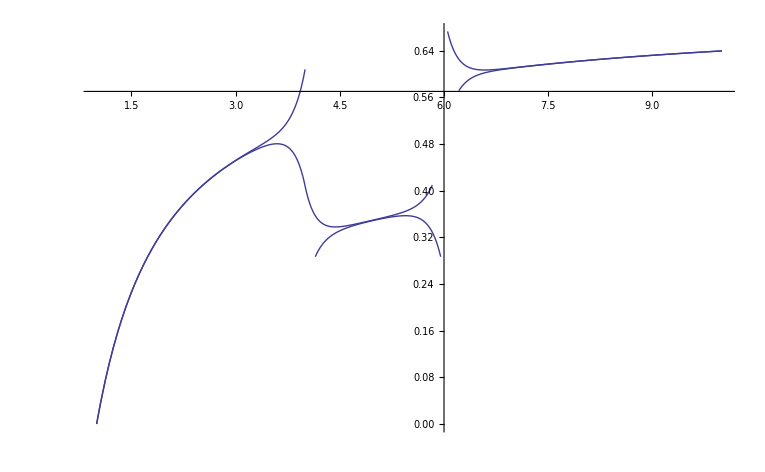

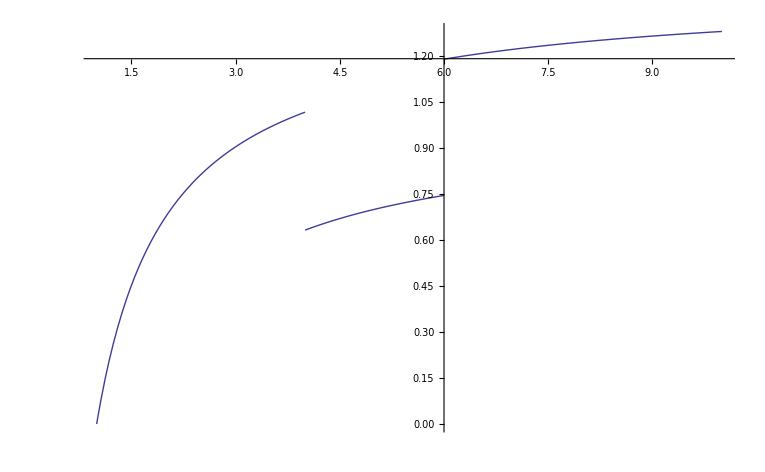

```mathematica
p1 = Plot[rho3[r], {r,b,10}];
p2 = Plot[rho2[r], {r,a,b}];
p3 = Plot[rho1[r], {r,rs,a}];
p4 = Plot[rhom3[r], {r,b,10}];
p5 = Plot[rhom2[r], {r,a,b}];
p6 = Plot[rhom1[r], {r,rs,a}];
Show[p1,p2,p3, PlotRange -> All]
Show[p4,p5,p6, PlotRange -> All]
```

```mathematica
Simplify[rhodash1[rs]]
N[rhodash1[a]-invs.bcu.s.rhodash2[a]]
N[invs.bcu.s.rhodash2[b]-rhodash3[b]]
N[rhodash1'[a]-rhodash2'[a]]
N[rhodash2'[b]-rhodash3'[b]]
Simplify[rhodash3[Infinity]]
```

{{0.},{0.}}

{{1.11022×10^-16},{-2.77556×10^-17}}

{{1.11022×10^-15},{1.08247×10^-15}}

{{3.46945×10^-17},{1.11022×10^-16}}

{{6.93889×10^-18},{1.44329×10^-14}}

{{1.},{0.}}

```mathematica
Total[rho1'[rs]]/Total[rho3[Infinity]]
```

{0.957747}